# Particle Diffusion

Michael Jones and Ian Jackson

```mathematica
Clear["`*"]
Needs["Units`"]
```

Start by creating a GUI window

```mathematica
DynamicModule[{f,p},f[g_]:=Graphics[g,ImageSize->Tiny];{SetterBar[Dynamic[p],{Disk[]->Disk,Rectangle[]->Rectangle}],Dynamic[f[p]]}]
```

2D draw path function

```mathematica
drawPath2D[a_,num_,c_,l_,w_]:=Module[{R,σ,width,height,objectX,objectY,V,λ,collisions,pathLength,pathAngle,coordinates,index,newX,newY,distance},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
σ=Pi R^2;
width=w;
height=l;
objectX=width/2;
objectY=height/2;
V=width height (2 R);
n=num/V;
λ=1/(n σ);
collisions=c;
pathLength={};
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions];
coordinates={{objectX,objectY}};
index=1;
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngle[[index]]];
newY=coordinates[[index,2]]+pathLength[[index]] Sin[pathAngle[[index]]];
coordinates=Append[coordinates,{newX,newY}];
index++;,
collisions];
distance=EuclideanDistance[coordinates[[1]],coordinates[[collisions+1]]];
{Graphics[{{Black,Line[coordinates]},{Red,Line[{coordinates[[1]],coordinates[[collisions+1]]}]}},Frame->True,PlotRange->{{0,width},{0,height}}],distance}
]
```

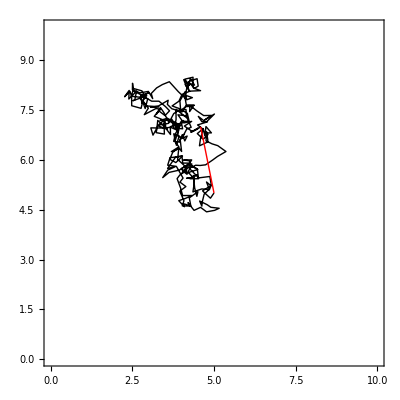

2.02947

```mathematica
{plot,distance}=drawPath2D["Hydrogen",5000000,300,10,10];
plot
distance
```

3D draw path function

```mathematica
drawPath3D[a_,num_,c_,l_,w_,d_]:=Module[{R,σ,width,height,depth,objectX,objectY,objectZ,V,λ,collisions,pathLength,pathAngle,pathAngleVert,coordinates,index,newX,newY,newZ,distance},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
σ=Pi R^2;
width=w;
height=l;
depth=d;
objectX=width/2;
objectY=height/2;
objectZ=depth/2;
V=width height depth;
n=num/V;
λ=1/(n σ);
collisions=c;
pathLength={};
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions];
pathAngleVert=RandomReal[{-Pi/2,Pi/2},collisions];
coordinates={{objectX,objectY,objectZ}};
index=1;
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Cos[pathAngle[[index]]];
newY=coordinates[[index,2]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Sin[pathAngle[[index]]];
newZ=coordinates[[index,3]]+pathLength[[index]] Sin[pathAngleVert[[index]]];
coordinates=Append[coordinates,{newX,newY,newZ}];
index++;,
collisions];
distance=EuclideanDistance[coordinates[[1]],coordinates[[collisions+1]]];
{Graphics3D[{{Black,Line[coordinates]},{Red,Line[{coordinates[[1]],coordinates[[collisions+1]]}]}},PlotRange->{{0,width},{0,height},{0,depth}}],distance}
]
```

```mathematica
{plot,distance}=drawPath3D["Hydrogen",750000000000,300,10,10,10];
plot
distance
```

-Graphics3D-

2.79537

```mathematica
calculateDrms3D[a_,num_,c_,l_,w_,d_]:=Module[{R,V,n,σ,λ},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
V=l w d;
n=num/V;
σ=Pi R^2;
λ=1/(n σ);
Sqrt[c] λ
]
```

```mathematica
calculateDrms3D["Hydrogen",750000000000,300,10,10,10]
```

3.

```mathematica
calculateDrms2D[a_,num_,c_,l_,w_]:=Module[{R,V,n,σ,λ},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
V=l w 2 R;
n=num/V;
σ=Pi R^2;
λ=1/(n σ);
Sqrt[c] λ
]
```

```mathematica
calculateDrms2D["Hydrogen",5000000,300,10,10]
```

4.